En todos nuestros problemas, queremos analizar las raízes de la función. Como se puede observar en la gráfica, esta función será problemática para algunos de los métodos en los puntos cerca del 0, que es un mínimo, y cerca del 1.8, un máximo. 
f[x_] := (x^2-2) Exp[-x^2]

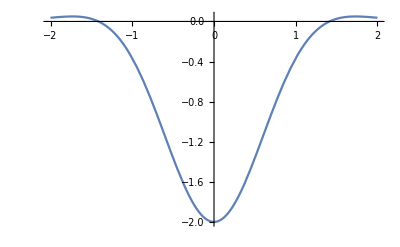

```mathematica
Plot[f[x],{x,-2,2}]
```

Trivialmente, la función tiene raíz apenas en los puntos , y lo podemos verificar con Mathematica tanto simbolica cuanto numericamente:

```mathematica
f[x_]:= (x^2-2) Exp[-x^2]
Solve[f[x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-√2},{x→√2}}

{{x→-√2},{x→√2}}
NSolve[f[x]==0,x]

{{x→-√2},{x→√2}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-1.41421},{x→1.41421}}

## Método de la Bisección

Para el método de la Bisección, implementamos con nuestro programa. Para los inputs sugeridos en el problema (Tolerancia = 1d-6, a = 0, b=2), tenemos este output:
-Graphics-
O sea, en 21 iteraciones convergimos a 1.41421413. Si comparamos este con el valor de la aproximación numérica de Mathematica con la misma precisión, veremos que obtuvimos el mismo resultado:

```mathematica
FindRoot[f[x]==0,{x,1}, AccuracyGoal->6,MaxIterations->1000]
```

{x→1.41421}

Pero es importante mencionar que tuvimos una convergencia lenta (comparada con los otros algoritmos).

## Método de Newton-Raphson

Implementamos el Método de Newton-Raphson en FORTRAN con nuestro programa. De donde utilizamos la derivada calculada en Mathematica:

```mathematica
f'[x]
```

2 ⅇ^(-x^2) x-2 ⅇ^(-x^2) x (-2+x^2)

Para los datos iniciales sugeridos en el problema (Tolerancia=1d-6, x0=1 y después x0=2), tenemos que:
-Graphics-
Que, si comparamos con el de Mathematica, vemos que es igual:

```mathematica
FindRoot[f[x]==0,{x,1}, AccuracyGoal->6,MaxIterations->1000]
```

FindRoot::nlnum: The function value {f[1.]} is not a list of numbers with dimensions {1} at {x} = {1.}.

FindRoot[f[x]==0,{x,1},AccuracyGoal→6,MaxIterations→1000]

Para el caso de x0=2, vemos que el método no converge a una raíz:

-Graphics-
En Mathematica, lo que tenemos es que va a un punto que no es raíz, pero que está suficientemente cerca del 0 para que la precisión de máquina no las pueda distinguir (Eso pasa porque la función exponencial decae suficientemente rápido):

```mathematica
FindRoot[f[x]==0,{x,2}, AccuracyGoal->6,MaxIterations->1000]
```

FindRoot::bddir: The search direction {0.0257543} is not a descent direction for the merit function. The step will be taken without the line search.

FindRoot::bddir: The search direction {0.0257201} is not a descent direction for the merit function. The step will be taken without the line search.

FindRoot::bddir: The search direction {0.025686} is not a descent direction for the merit function. The step will be taken without the line search.

General::stop: Further output of FindRoot::bddir will be suppressed during this calculation.

{x→27.2904}

```mathematica
f[x]/.x->27.2904
```

General::munfl: Exp[-744.766] is too small to represent as a normalized machine number; precision may be lost.

0.

Si no abortáramos para derivadas muy próximas del 0 (a menos de 1d-6 de 0) ‘convergiríamos’ a este mismo valor de 27.29.

## Metódo de la Secante

Del mismo modo que los otros, implementamos el método de la secante. Igual que en el de Newton, si la ‘derivada’ (en este caso, la diferencia finita) es muy próxima de 0, abortamos el programa.

Cuando ponemos las condiciones iniciales sugeridas (tolerancia=1d-6, x0=0,x1=2) tenemos que:
-Graphics-
Y eso es esperado, ya que el 0 es un mínimo de la función y ‘debería’ ser un punto horrible para este método. Si cambiamos los valores iniciales a unos un poco diferentes, ya converge.
-Graphics-
No obstante, implementamos un programa que, cuando tengamos ‘malos valores’ durante el método de secante que utilize un método ‘regularizado’, conocido como regula falsi. Basicamente, mezclamos el método de secantes con el de bisección, y de esa forma estamos garantizados a llegar una raíz. El único problema es que puede tardar más que el de la bisección, especialmente para casos patológicos como el intervalo en que estamos trabajando.Con este método, tenemos que:

-Graphics-